## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW151226";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={};
mergerParams={};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

Part::partw: Part 5 of Missing[KeyAbsent,dalpha_3] does not exist.

```mathematica
samples
```

```mathematica
raw=Import[FileNameJoin[{baseDir,eventID,"GR"<>"_IMRP_posterior.csv"}]];
samples["GR"]=(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]](*spin2z*)};
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
vsPlots=<||>;
vsPlots["p2p4"]={};
```

## INSPIRAL

```mathematica
contourPoints
```

contourPoints

### phi_2 v.s. phi_4

```mathematica
p="GR"
m1Data=samples["GR"][[1]];
m2Data=samples["GR"][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.001643};
contourPD[p]={0.025};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*) 
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

GR

输入Mc范围：{3,40}

输入q范围：{1,3}

m1范围：{3.4461,81.9069}

m2范围：{2.04767,45.9479}

对称数据：原始 52060 + 镜像 52060

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.025}，共 2 条

第一条前3点：{{15.0522,6.74466},{15.1023,6.73739},{15.1692,6.72769}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.299854

可信水平百分比：29.9854%

==========================

GR 预处理完成，红线包含概率 prob = 0.299854

```mathematica
contourPoints
```

contourPoints

```mathematica
probability=prob;
(*probability=0.05;*)
temp=PlotInversion["dphi_2",probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.350073, 0.649927}

实际使用的 GR 概率区间上下界: {6.20892, 6.36337}

实际使用的 Param 概率区间上下界: {5.77538, 6.59353}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=2.29881×10^-16

GR上界: 点数=170 | Y>0点数=170 | 平均误差=9.45649×10^-16

Param下界: 点数=170 | Y>0点数=170 | 平均误差=4.12742×10^-16

Param上界: 点数=170 | Y>0点数=170 | 平均误差=0.151734

{{3.1,15.1597},{3.2,15.6488},{3.3,16.1378},{3.4,16.6268},{3.5,17.1158}}

{{3.1,3.1},{3.2,3.2},{3.3,3.3},{3.4,3.4},{3.5,3.5}}

chi1L取值：0.614549

chi2L取值：0.529968

=====================================================

Part::partw: Part {1,2} of contourPoints[dphi_2] does not exist.

Part::partw: Part {2,1} of contourPoints[dphi_2] does not exist.

ListLinePlot::lpn: {{},{{15.1597,3.1},{15.6488,3.2},{16.1378,3.3},{16.6268,3.4},{17.1158,3.5},{17.6049,3.6},{18.0939,3.7},{18.5829,3.8},{19.0719,3.9},{19.561,4.},«160»},{{3.1,3.1},{3.2,3.2},{3.3,3.3},{3.4,3.4},{3.5,3.5},{3.6,3.6},{3.7,3.7},{3.8,3.8},{3.9,3.9},{3.99999,4.},«160»}} is not a list of numbers or pairs of numbers.

ListLinePlot[{contourPoints[dphi_2]⟦{2,1}⟧,{{15.1597,3.1},{15.6488,3.2},{16.1378,3.3},{16.6268,3.4},{17.1158,3.5},{17.6049,3.6},{18.0939,3.7},{18.5829,3.8},{19.0719,3.9},{19.561,4.},{20.05,4.1},{20.539,4.2},{21.028,4.3},{21.5171,4.4},{22.0061,4.5},{22.4951,4.6},{22.9841,4.7},{23.4731,4.8},{23.9622,4.9},{24.4512,5.},{24.9402,5.1},{25.4292,5.2},{25.9183,5.3},{26.4073,5.4},{26.8963,5.5},{27.3853,5.6},{27.8744,5.7},{28.3634,5.8},{28.8524,5.9},{29.3414,6.},{29.8305,6.1},{30.3195,6.2},{30.8085,6.3},{31.2975,6.4},{31.7866,6.5},{32.2756,6.6},{32.7646,6.7},{33.2536,6.8},{33.7426,6.9},{34.2317,7.},{34.7207,7.1},{35.2097,7.2},{35.6987,7.3},{36.1878,7.4},{36.6768,7.5},{37.1658,7.6},{37.6548,7.7},{38.1439,7.8},{38.6329,7.9},{39.1219,8.},{39.6109,8.1},{40.1,8.2},{40.589,8.3},{41.078,8.4},{41.567,8.5},{42.0561,8.6},{42.5451,8.7},{43.0341,8.8},{43.5231,8.9},{44.0121,9.},{44.5012,9.1},{44.9902,9.2},{45.4792,9.3},{45.9682,9.4},{46.4573,9.5},{46.9463,9.6},{47.4353,9.7},{47.9243,9.8},{48.4134,9.9},{48.9024,10.},{49.3914,10.1},{49.8804,10.2},{50.3695,10.3},{50.8585,10.4},{51.3475,10.5},{51.8365,10.6},{52.3256,10.7},{52.8146,10.8},{53.3036,10.9},{53.7926,11.},{54.2816,11.1},{54.7707,11.2},{55.2597,11.3},{55.7487,11.4},{56.2377,11.5},{56.7268,11.6},{57.2158,11.7},{57.7048,11.8},{58.1938,11.9},{58.6829,12.},{59.1719,12.1},{59.6609,12.2},{60.1499,12.3},{60.639,12.4},{61.128,12.5},{61.617,12.6},{62.106,12.7},{62.5951,12.8},{63.0841,12.9},{63.5731,13.},{64.0621,13.1},{64.5512,13.2},{65.0402,13.3},{65.5292,13.4},{66.0182,13.5},{66.5072,13.6},{66.9963,13.7},{67.4853,13.8},{67.9743,13.9},{68.4633,14.},{68.9524,14.1},{69.4414,14.2},{69.9304,14.3},{70.4194,14.4},{70.9085,14.5},{71.3975,14.6},{71.8865,14.7},{72.3755,14.8},{72.8646,14.9},{73.3536,15.},{73.8426,15.1},{74.3316,15.2},{74.8207,15.3},{75.3097,15.4},{75.7987,15.5},{76.2877,15.6},{76.7767,15.7},{77.2658,15.8},{77.7548,15.9},{78.2438,16.},{78.7328,16.1},{79.2219,16.2},{79.7109,16.3},{80.1999,16.4},{80.6889,16.5},{81.178,16.6},{81.667,16.7},{82.156,16.8},{82.645,16.9},{83.1341,17.},{83.6231,17.1},{84.1121,17.2},{84.6011,17.3},{85.0902,17.4},{85.5792,17.5},{86.0682,17.6},{86.5572,17.7},{87.0462,17.8},{87.5353,17.9},{88.0243,18.},{88.5133,18.1},{89.0023,18.2},{89.4914,18.3},{89.9804,18.4},{90.4694,18.5},{90.9584,18.6},{91.4475,18.7},{91.9365,18.8},{92.4255,18.9},{92.9145,19.},{93.4036,19.1},{93.8926,19.2},{94.3816,19.3},{94.8706,19.4},{95.3597,19.5},{95.8487,19.6},{96.3377,19.7},{96.8267,19.8},{97.3158,19.9},{97.8048,20.}},{{3.1,3.1},{3.2,3.2},{3.3,3.3},{3.4,3.4},{3.5,3.5},{3.6,3.6},{3.7,3.7},{3.8,3.8},{3.9,3.9},{3.99999,4.},{4.1,4.1},{4.2,4.2},{4.3,4.3},{4.40001,4.4},{4.50001,4.5},{4.6,4.6},{4.7,4.7},{4.8,4.8},{4.9,4.9},{5.,5.},{5.10001,5.1},{5.19999,5.2},{5.30001,5.3},{5.39999,5.4},{5.50001,5.5},{5.59999,5.6},{5.69999,5.7},{5.79999,5.8},{5.89999,5.9},{5.99999,6.},{6.09999,6.1},{6.19999,6.2},{6.30001,6.3},{6.4,6.4},{6.49999,6.5},{6.6,6.6},{6.69999,6.7},{6.80001,6.8},{6.9,6.9},{7.,7.},{7.1,7.1},{7.20001,7.2},{7.29999,7.3},{7.4,7.4},{7.49999,7.5},{7.60001,7.6},{7.69999,7.7},{7.80001,7.8},{7.89999,7.9},{7.99999,8.},{8.1,8.1},{8.20001,8.2},{8.3,8.3},{8.39999,8.4},{8.49999,8.5},{8.6,8.6},{8.69999,8.7},{8.79999,8.8},{8.9,8.9},{8.99999,9.},{9.09999,9.1},{9.19999,9.2},{9.30001,9.3},{9.40001,9.4},{9.49999,9.5},{9.59999,9.6},{9.7,9.7},{9.80001,9.8},{9.90002,9.9},{9.99999,10.},{10.1,10.1},{10.2,10.2},{10.3,10.3},{10.4,10.4},{10.5,10.5},{10.6,10.6},{10.7,10.7},{10.8,10.8},{10.9,10.9},{11.,11.},{11.1,11.1},{11.2,11.2},{11.3,11.3},{11.4,11.4},{11.5,11.5},{11.6,11.6},{11.7,11.7},{11.8,11.8},{11.9,11.9},{12.,12.},{12.1,12.1},{12.2,12.2},{12.3,12.3},{12.4,12.4},{12.5,12.5},{12.6,12.6},{12.7,12.7},{12.8,12.8},{12.9,12.9},{13.,13.},{13.1,13.1},{13.2,13.2},{13.3,13.3},{13.4,13.4},{13.5,13.5},{13.6,13.6},{13.7,13.7},{13.8,13.8},{13.9,13.9},{14.,14.},{14.1,14.1},{14.2,14.2},{14.3,14.3},{14.4,14.4},{14.5,14.5},{14.6,14.6},{14.7,14.7},{14.8,14.8},{14.9,14.9},{15.,15.},{15.1,15.1},{15.2,15.2},{15.3,15.3},{15.4,15.4},{15.5,15.5},{15.6,15.6},{15.7,15.7},{15.8,15.8},{15.9,15.9},{16.,16.},{16.1,16.1},{16.2,16.2},{16.3,16.3},{16.4,16.4},{16.5,16.5},{16.6,16.6},{16.7,16.7},{16.8,16.8},{16.9,16.9},{17.,17.},{17.1,17.1},{17.2,17.2},{17.3,17.3},{17.4,17.4},{17.5,17.5},{17.6,17.6},{17.7,17.7},{17.8,17.8},{17.9,17.9},{18.,18.},{18.1,18.1},{18.2,18.2},{18.3,18.3},{18.4,18.4},{18.5,18.5},{18.6,18.6},{18.7,18.7},{18.8,18.8},{18.9,18.9},{19.,19.},{19.1,19.1},{19.2,19.2},{19.3,19.3},{19.4,19.4},{19.5,19.5},{19.6,19.6},{19.7,19.7},{19.8,19.8},{19.9,19.9},{20.,20.}}},PlotStyle→{RGBColor[1, 0, 0],Directive[RGBColor[0.5, 0, 0.5],Opacity[1]],Directive[RGBColor[0.5, 0, 0.5],Opacity[1]]},Axes→False,Frame→True,FrameLabel→{m_1/m_☉,m_2/m_☉},FrameStyle→Directive[GrayLevel[0],Thickness[0.004]],BaseStyle→{FontSize→15},AspectRatio→1,PlotRange→{{3.,20.},{3.,20.}},Epilog→{{Directive[RGBColor[0.5, 0, 0.5],Opacity[0.2]],Polygon[…]},{GrayLevel[1],Polygon[…]},{Directive[GrayLevel[0],Dashing[{Small,Small}],Opacity[1]],Line[{{3.,3.},{20.,20.}}]},Inset[-Graphics-  m_1-m_2
-Graphics-  ϕ_(2,NS)^(par)
-Graphics-  m_1 = m_2,Scaled[{0.35,0.82}]]},PlotLabel→p_c==0.2999,ImageSize→Medium,ImageMargins→{{5,5},{5,5}}]

```mathematica
AppendTo[vsPlots["p2p4"],temp];
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.0345, 0.9655}

实际使用的 GR 概率区间上下界: {43.6686, 46.2435}

实际使用的 Param 概率区间上下界: {-121.589, 45.2369}

GR下界: 点数=500 | Y>0点数=500 | 平均误差=8.3844×10^-16

GR上界: 点数=500 | Y>0点数=500 | 平均误差=1.08429×10^-14

Param下界: 点数=500 | Y>0点数=500 | 平均误差=151.693

Param上界: 点数=500 | Y>0点数=500 | 平均误差=7.10543×10^-15

{{10.1,358580.},{10.2,362131.},{10.3,365682.},{10.4,369231.},{10.5,372782.}}

{{10.1,16.2168},{10.2,16.3774},{10.3,16.538},{10.4,16.6985},{10.5,16.8591}}

chi1L取值：0.262031

chi2L取值：0.383743

=====================================================

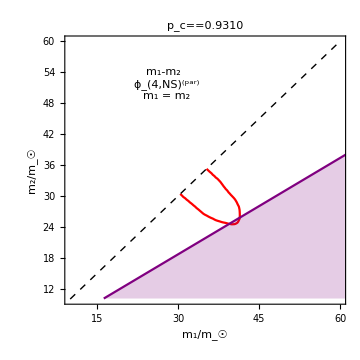

```mathematica
probability=prob;
probability=0.9310;

temp=PlotInversion["dphi_4",probability,10,60,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

```mathematica
AppendTo[vsPlots["p2p4"],temp];
```

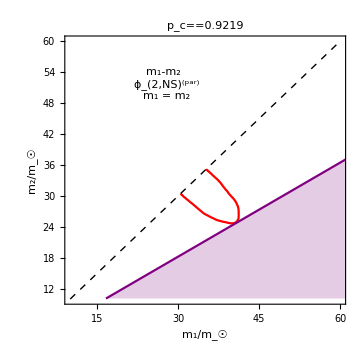
{-Graphics-,-Graphics-}

```mathematica
vsPlots["p2p4"]
```

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.02515};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

输入Mc范围：{3,40}

输入q范围：{1,3}

m1范围：{3.4461,81.9069}

m2范围：{2.04767,45.9479}

对称数据：原始 22848 + 镜像 22848

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999989（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.02515}，共 4 条

第一条前3点：{{14.0403,7.34002},{14.0505,7.27336},{14.0819,7.24836}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.0699159

可信水平百分比：6.99159%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.0699159

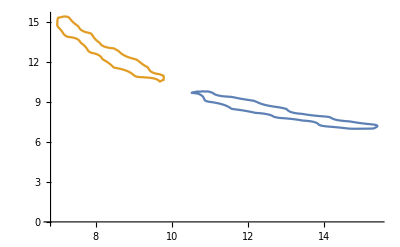

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.465042, 0.534958}

实际使用的 GR 概率区间上下界: {6.27102, 6.3079}

实际使用的 Param 概率区间上下界: {6.06146, 6.24786}

GR下界: 点数=27 | Y>0点数=27 | 平均误差=1.97373×10^-16

GR上界: 点数=27 | Y>0点数=27 | 平均误差=8.22387×10^-16

Param下界: 点数=27 | Y>0点数=27 | 平均误差=1.64477×10^-16

Param上界: 点数=27 | Y>0点数=27 | 平均误差=3.94746×10^-16

{{4,11.9664},{5,14.958},{6,17.9496},{7,20.9412},{8,23.9328}}

{{4,1.89845},{5,2.37307},{6,2.84768},{7,3.32229},{8,3.79691}}

chi1L取值：0.614549

chi2L取值：0.529968

=====================================================

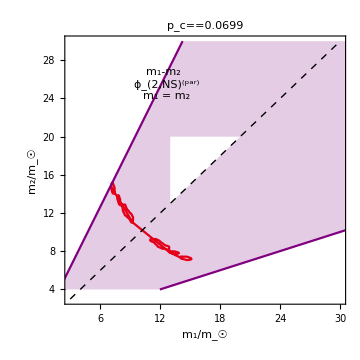

```mathematica
probability=prob;
(*probability=0.05;
*)
(*probability=0.085;*)

PlotInversion[p,probability,3,30,1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3,4}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0198};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 22184 + 镜像 22184

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0198}，共 2 条

第一条前3点：{{9.43812,9.94153},{9.38601,9.99432},{9.32587,10.0577}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.553344

可信水平百分比：55.3344%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.553344

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

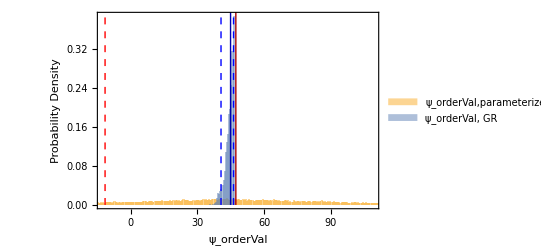

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.48825, 0.51175}

实际使用的 GR 概率区间上下界: {44.8374, 44.9419}

实际使用的 Param 概率区间上下界: {46.2448, 48.34}

GR下界: 点数=27 | Y>0点数=27 | 平均误差=1.84215×10^-15

GR上界: 点数=27 | Y>0点数=27 | 平均误差=5.00012×10^-15

Param下界: 点数=27 | Y>0点数=27 | 平均误差=7.89492×10^-16

Param上界: 点数=27 | Y>0点数=0 | 平均误差=2.10531×10^-14

{{4,3.94061},{5,4.92576},{6,5.91091},{7,6.89606},{8,7.88121}}

{{4,-8.78576},{5,-10.9822},{6,-13.1786},{7,-15.3751},{8,-17.5715}}

chi1L取值：0.569676

chi2L取值：0.495363

=====================================================

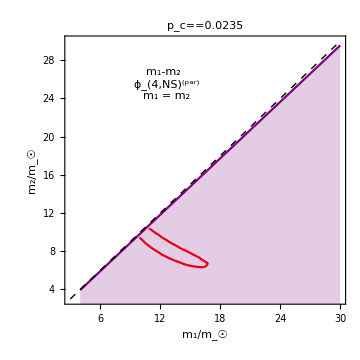

```mathematica
probability=prob;
(*probability=0.0235;*)
probability=0.0235;

PlotInversion[p,probability,3,30,1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
(*contourPD[p]={0.032};*)
contourPD[p]={0.0323};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,3}

m1范围：{3.4461,81.9069}

m2范围：{2.04767,45.9479}

对称数据：原始 37274 + 镜像 37274

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 81.9069} × {2.04767, 81.9069}

等高线值：{0.0323}，共 2 条

第一条前3点：{{10.2717,10.0222},{10.2387,9.95918},{10.2313,9.94311}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.198459

可信水平百分比：19.8459%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.198459

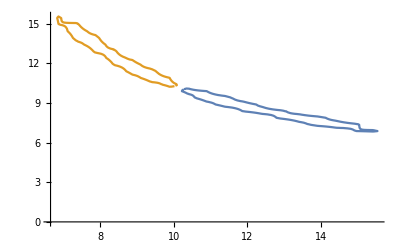

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

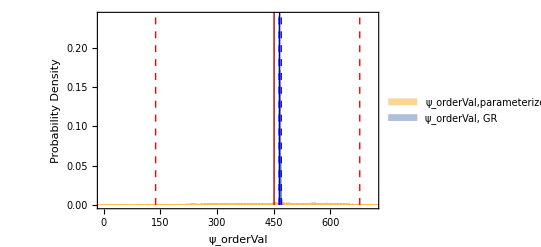

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.46745, 0.53255}

实际使用的 GR 概率区间上下界: {465.946, 466.235}

实际使用的 Param 概率区间上下界: {436.979, 464.773}

GR下界: 点数=110 | Y>0点数=110 | 平均误差=5.68434×10^-14

GR上界: 点数=110 | Y>0点数=110 | 平均误差=1.86033×10^-14

Param下界: 点数=110 | Y>0点数=110 | 平均误差=27.7777

Param上界: 点数=110 | Y>0点数=110 | 平均误差=5.68434×10^-15

{{3.2,3.20006},{3.4,3.40008},{3.6,3.60002},{3.8,3.80004},{4.,3.99992}}

{{3.2,3.00584},{3.4,3.1937},{3.6,3.38157},{3.8,3.56943},{4.,3.7573}}

chi1L取值：0.556081

chi2L取值：0.549942

=====================================================

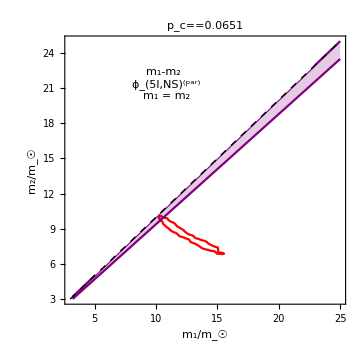

```mathematica
probability=prob;
(*probability=0.1302;*)
probability=0.0651;

PlotInversion[p,probability,3,25,0.2,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0301};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 33798 + 镜像 33798

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0301}，共 2 条

第一条前3点：{{13.5153,7.46743},{13.5803,7.43387},{13.6252,7.40868}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.113761

可信水平百分比：11.3761%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.113761

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

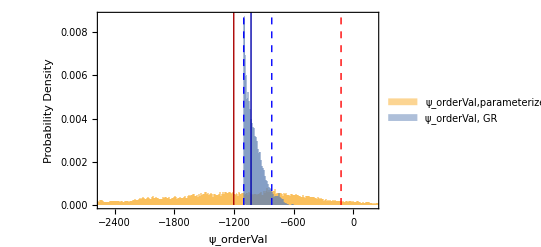

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.44312, 0.55688}

实际使用的 GR 概率区间上下界: {-1041.89, -1014.73}

实际使用的 Param 概率区间上下界: {-1307.9, -1089.6}

GR下界: 点数=370 | Y>0点数=370 | 平均误差=1.12458×10^-13

GR上界: 点数=370 | Y>0点数=370 | 平均误差=9.40221×10^-14

Param下界: 点数=370 | Y>0点数=370 | 平均误差=203.778

Param上界: 点数=370 | Y>0点数=370 | 平均误差=1.28435×10^-13

{{3.1,3.10001},{3.2,3.2},{3.3,3.29999},{3.4,3.4},{3.5,3.49999}}

{{3.1,2.3742},{3.2,2.45079},{3.3,2.52738},{3.4,2.60396},{3.5,2.68055}}

chi1L取值：0.531846

chi2L取值：0.440716

=====================================================

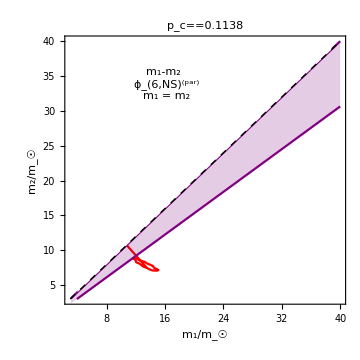

```mathematica
probability=prob;
(*probability=0.15;*)

PlotInversion[p,probability,3,40,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,30},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.030259};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,30}

输入q范围：{1,5}

m1范围：{3.4461,81.7221}

m2范围：{1.63444,34.461}

对称数据：原始 32222 + 镜像 32222

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 81.7221} × {1.63444, 81.7221}

等高线值：{0.030259}，共 4 条

第一条前3点：{{10.5032,9.62735},{10.473,9.66674},{10.4242,9.69696}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.159907

可信水平百分比：15.9907%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.159907

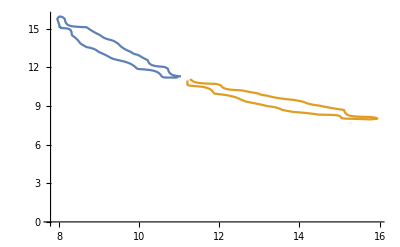

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

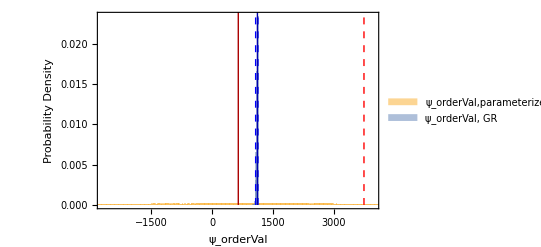

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.420047, 0.579953}

实际使用的 GR 概率区间上下界: {1114.63, 1121.79}

实际使用的 Param 概率区间上下界: {211.583, 1114.26}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=1.13687×10^-13

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.60499×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=741.932

Param上界: 点数=170 | Y>0点数=170 | 平均误差=6.82121×10^-14

{{3.1,328596.},{3.2,339194.},{3.3,349794.},{3.4,360395.},{3.5,370994.}}

{{3.1,1.58898},{3.2,1.64024},{3.3,1.69149},{3.4,1.74275},{3.5,1.79401}}

chi1L取值：0.552261

chi2L取值：0.528894

=====================================================

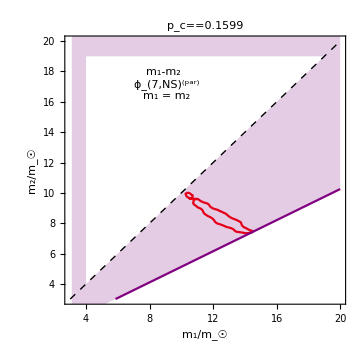

```mathematica
probability=prob;
(*probability=0.16;*)
(*probability=0.16;*)

PlotInversion[p,probability,3,20,0.1,cm->True,cd->False,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

# utils